# propto_omega

```mathematica
Quit[]
```

## (α̃)_B

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_propto_omega_B.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_propto_omega_B.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,alphaB}

```mathematica
dir="./Data/spectra_latin_hc_propto_omega_B/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 181.82018

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

12

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,2,3,5,6,7,8,9,10,11,12}

11

12

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{1,12,16,41,44,56,59,69,97,98,99}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{0.0644168,0.912945,0.46447}

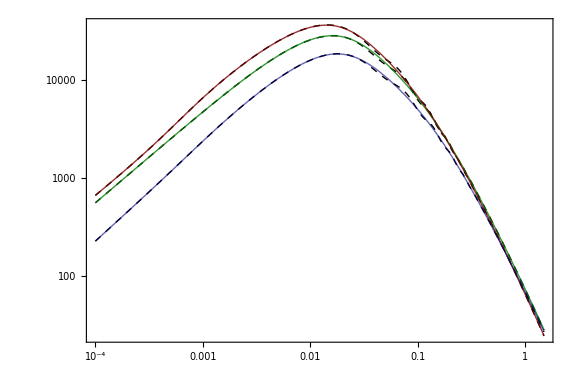

```mathematica
i=1;j=12;l=16;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 0.064"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 0.913"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 0.464"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

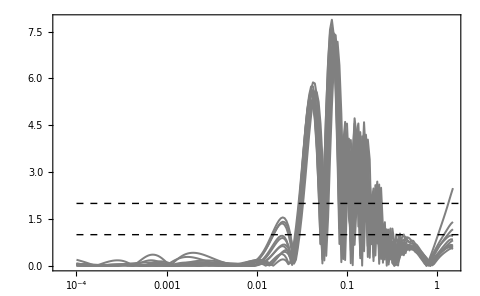

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{0.0644168,0.912945,0.46447}

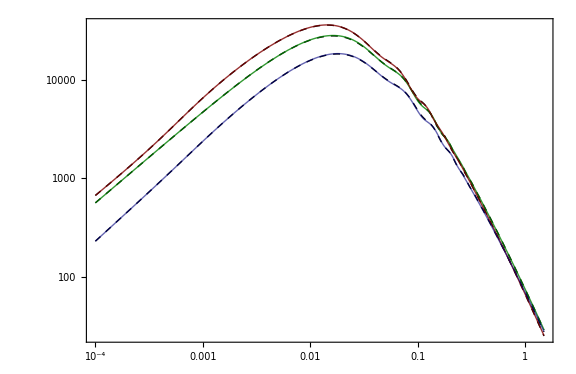

```mathematica
i=1;j=12;l=16;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 0.064"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 0.913"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_B = 0.464"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

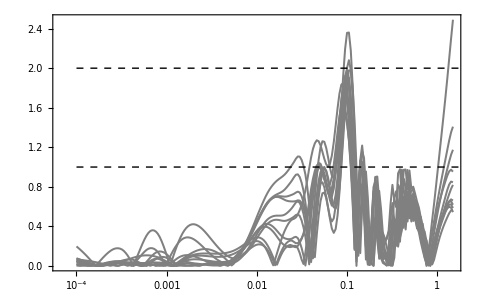

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]
```

## (α̃)_M

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_propto_omega_M.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_propto_omega_M.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,alphaM}

```mathematica
dir="./Data/spectra_latin_hc_propto_omega_M/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 161.80026

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

35

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,2,3,4,5,7,9,10,11,12,13,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,32,33,34,35}

31

35

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{1,9,10,12,16,26,38,40,41,42,44,50,54,55,56,59,63,64,67,69,70,72,74,79,82,88,95,97,98,99,100}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{0.103067,0.767905,1.22112}

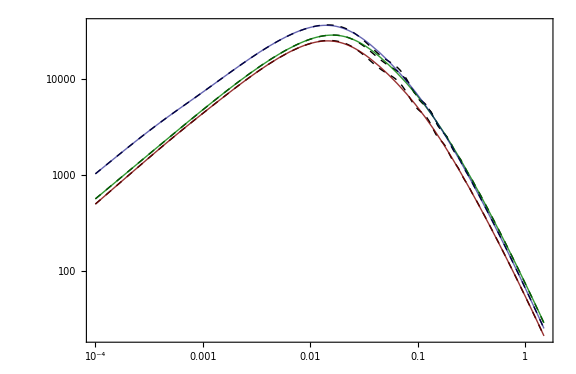

```mathematica
i=1;j=9;l=10;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 0.103"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 0.768"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 1.221"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

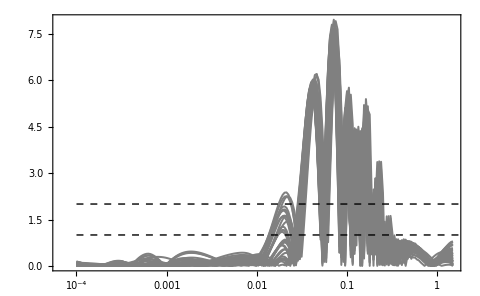

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{0.103067,0.767905,1.22112}

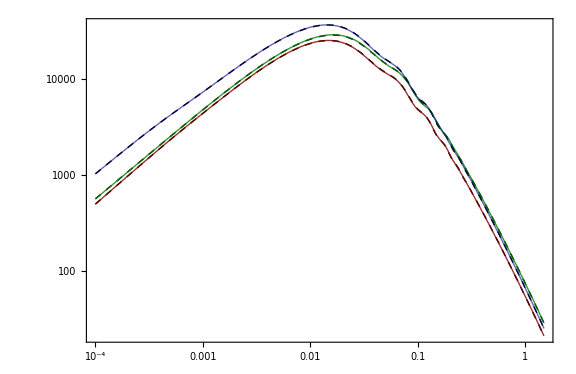

```mathematica
i=1;j=9;l=10;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 0.103"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 0.768"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_M = 1.221"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

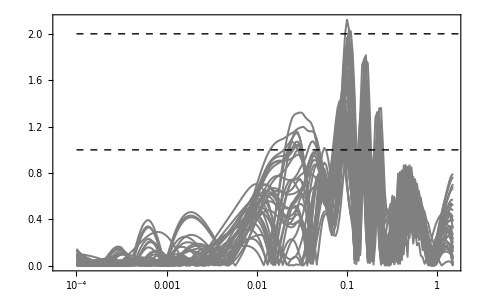

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

## (α̃)_T

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_propto_omega_T.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_propto_omega_T.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,alphaT}

```mathematica
dir="./Data/spectra_latin_hc_propto_omega_T/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 179.48373

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

35

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,2,3,4,5,6,7,8,10,11,12,13,14,15,16,17,18,19,20,22,23,24,25,26,28,29,30,32,33,34,35}

31

35

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{1,9,10,11,12,16,26,30,38,40,41,42,46,50,53,56,59,64,67,69,70,71,74,79,83,88,95,97,98,99,100}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{-0.974233,-0.808024,-0.694719}

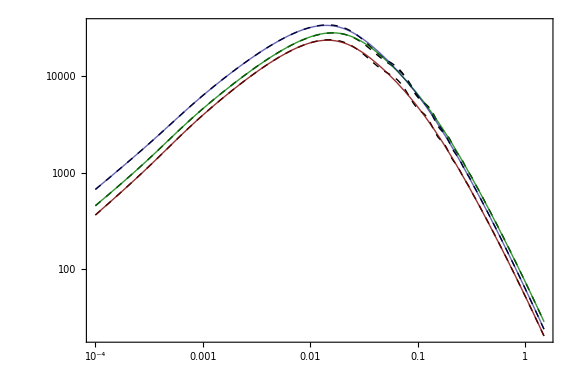

```mathematica
i=1;j=9;l=10;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.974"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.808"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.695"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

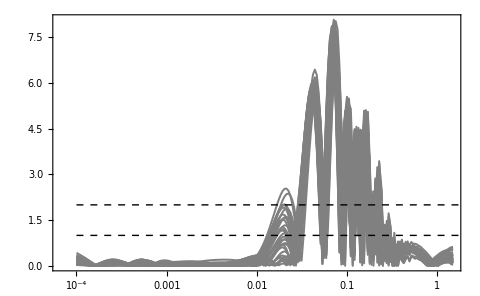

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{-0.974233,-0.808024,-0.694719}

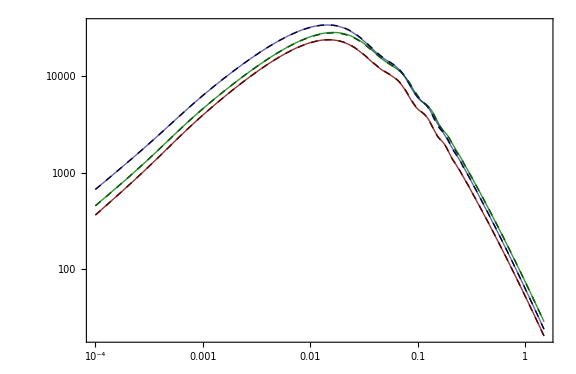

```mathematica
i=1;j=9;l=10;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.974"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.808"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{\\alpha}_T = -0.695"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

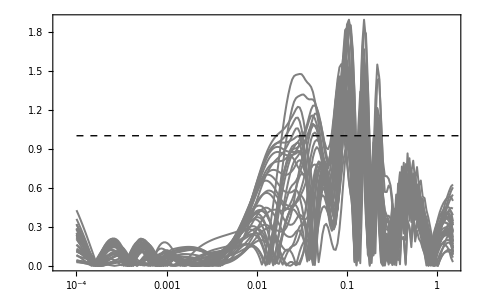

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

# propto_scale

```mathematica
Quit[]
```

## (α̂)_B

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_propto_scale_B.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_propto_scale_B.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,alphaB}

```mathematica
dir="./Data/spectra_latin_hc_propto_scale_B/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 182.03449

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

35

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,4,7,10,13,15,16,17,19,21,22,24,27,28,29,33,35}

17

35

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{1,12,26,30,41,44,46,48,50,54,59,65,79,82,85,98,100}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{0.01546,0.219107,0.00759846}

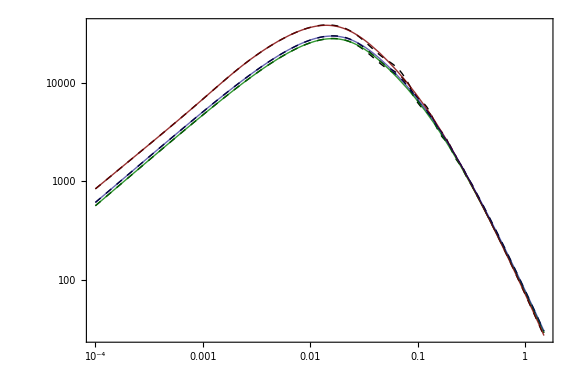

```mathematica
i=1;j=12;l=26;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[4,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[7,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.015"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.219"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.008"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

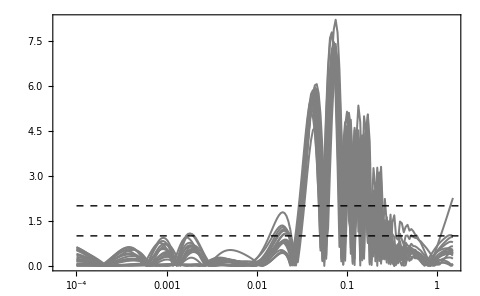

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{0.01546,0.219107,0.00759846}

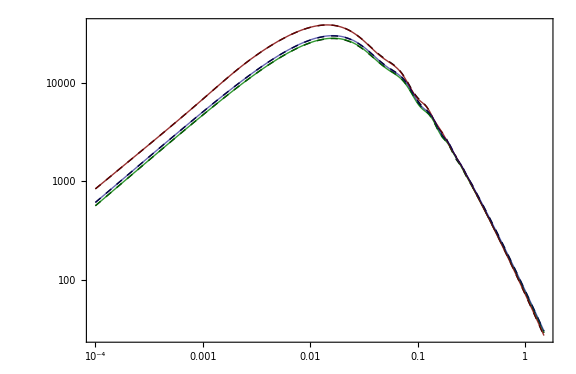

```mathematica
i=1;j=12;l=26;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[4,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[7,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.015"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.219"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.008"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

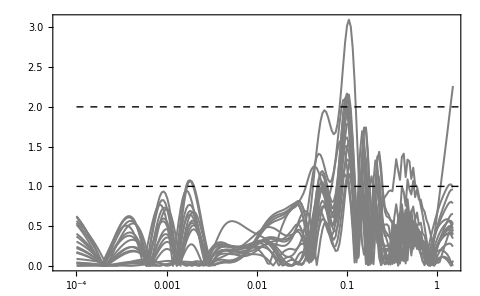

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]
```

## (α̂)_M

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_propto_scale_M.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_propto_scale_M.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,alphaM}

```mathematica
dir="./Data/spectra_latin_hc_propto_scale_M/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 186.10715

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

28

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,2,3,4,6,7,8,9,10,11,12,13,14,15,16,17,18,20,21,22,23,25,26,27,28}

25

28

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{1,10,12,16,26,31,41,42,44,46,50,51,54,56,59,65,67,74,79,82,88,97,98,99,100}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{0.0257667,0.305281,0.365178}

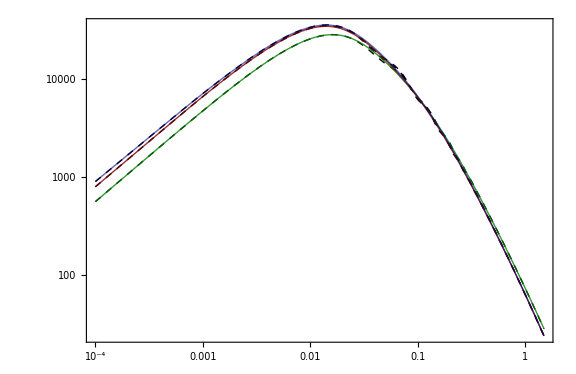

```mathematica
i=1;j=10;l=12;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.026"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.305"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.365"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

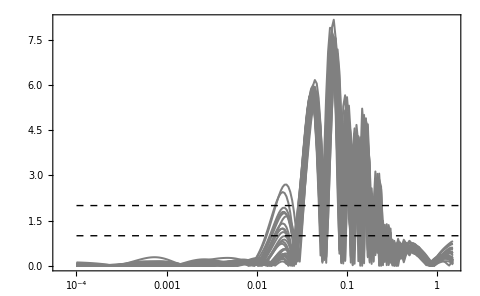

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{0.0257667,0.305281,0.365178}

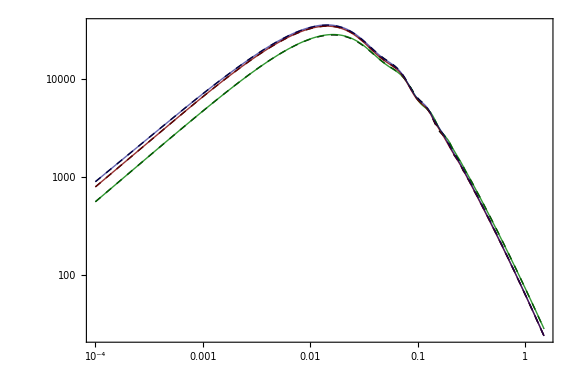

```mathematica
i=1;j=10;l=12;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.026"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.305"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.365"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

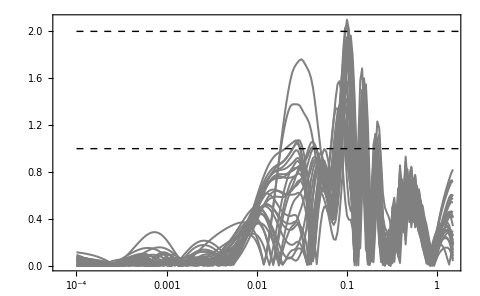

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]
```

## (α̂)_T

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_propto_scale_T.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_propto_scale_T.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,alphaT}

```mathematica
dir="./Data/spectra_latin_hc_propto_scale_T/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 154.14434

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

42

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,20,21,22,23,25,26,28,30,31,32,34,35,36,39,40,41,42}

33

42

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{1,9,10,12,16,17,18,26,30,38,40,41,42,44,46,50,53,54,56,59,64,67,69,71,74,79,82,83,88,97,98,99,100}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{-0.974233,-0.808024,-0.694719}

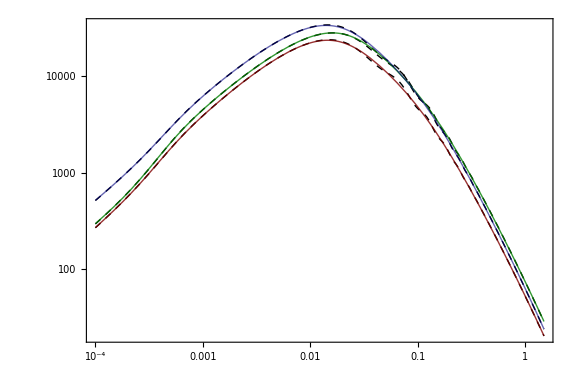

```mathematica
i=1;j=9;l=10;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[3,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[4,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.974"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.808"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.695"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

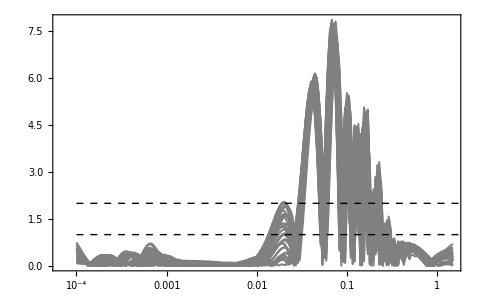

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{-0.974233,-0.808024,-0.694719}

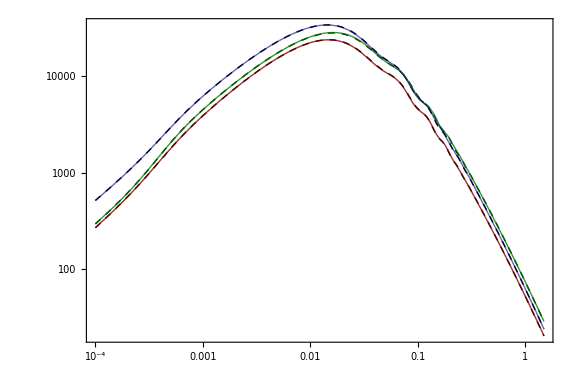

```mathematica
i=1;j=9;l=10;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[3,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[4,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.974"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.808"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.695"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

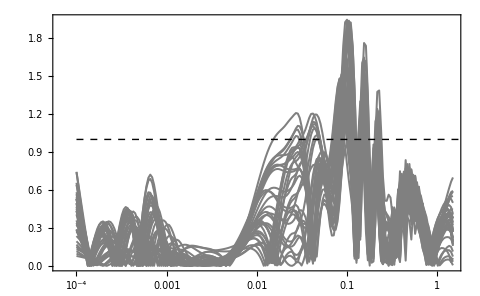

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

# Cubic Galileon

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_cubic_galileon.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_cubic_galileon.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As}

```mathematica
dir="./Data/spectra_latin_hc_cubic_galileon/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 145.99267

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

5

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.5&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,2,3,4,5}

5

5

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{17,33,37,55,65}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

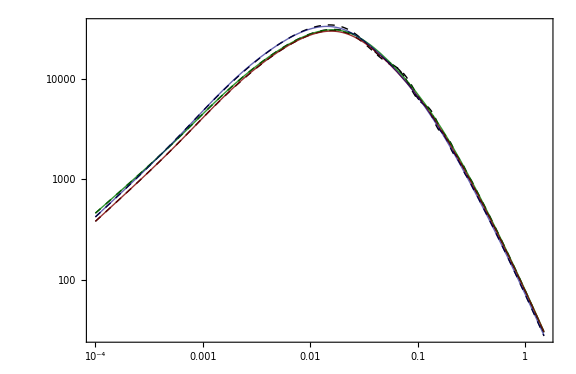

```mathematica
i=17;j=33;l=37;
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\text{Model} = 17"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\text{Model} = 33"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\text{Model} = 37"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

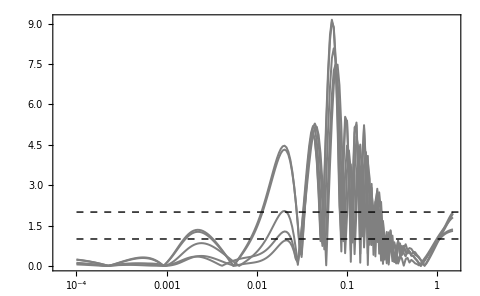

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

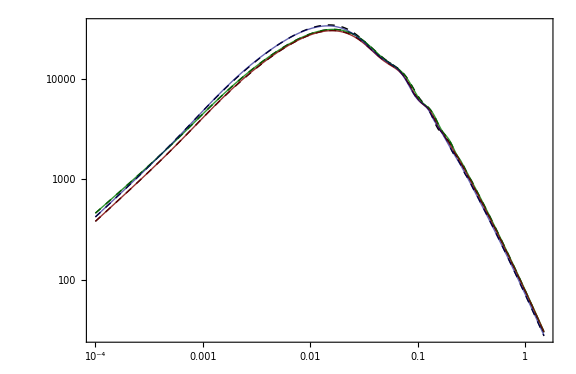

```mathematica
i=17;j=33;l=37;
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\text{Model} = 17"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\text{Model} = 33"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\text{Model} = 37"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

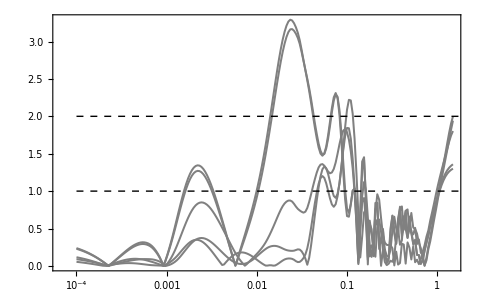

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

# Quartic Galileon

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_quartic_galileon.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_quartic_galileon.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,xi}

```mathematica
dir="./Data/spectra_latin_hc_quartic_galileon/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 111.63568

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

16

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,3,4,5,6,7,8,9,10,11,13,14,15,16}

14

16

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{1,8,10,12,18,19,21,22,26,33,40,44,49,50}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{2.39944,2.40461,2.39743}

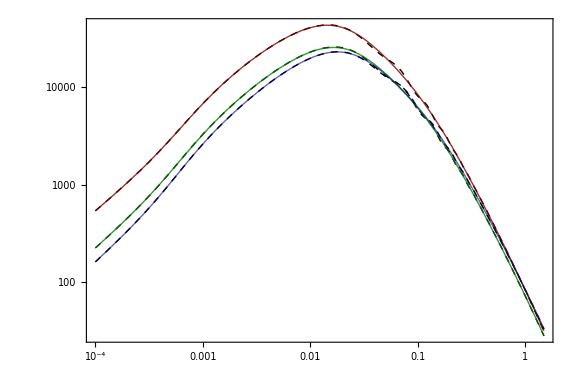

```mathematica
i=1;j=8;l=10;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[3,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[4,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\xi = 2.399"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\xi = 2.405"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\xi = 2.397"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

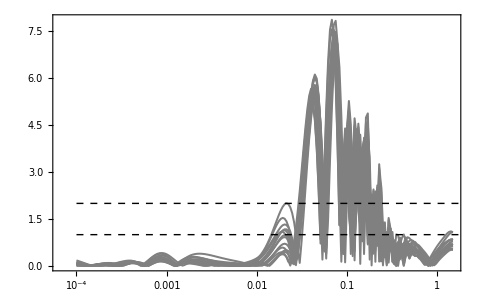

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{2.39944,2.40461,2.39743}

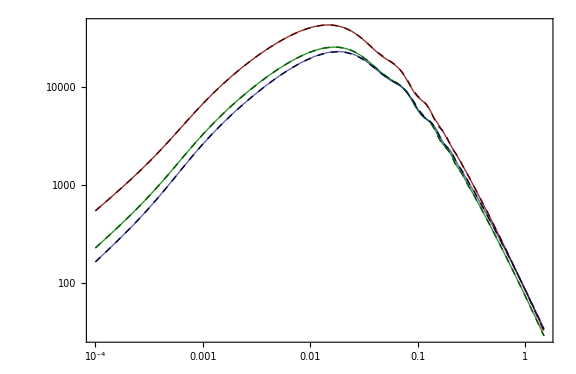

```mathematica
i=1;j=8;l=10;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[3,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[4,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\xi = 2.399"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\xi = 2.405"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\xi = 2.397"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

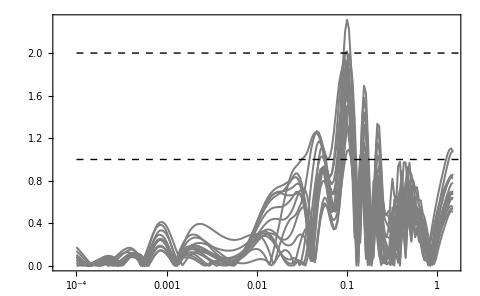

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]
```

# f(R)

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_fR.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_fR.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,log10fR0}

```mathematica
dir="./Data/spectra_latin_hc_fR/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2*(1+γ/(1+(kMG/k)^Δ))

Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 89.009048

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

93

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{1,2,3,4,8,9,10,11,13,14,15,17,19,23,25,27,32,35,36,37,38,39,40,42,44,46,49,50,52,55,59,60,61,63,65,66,67,68,69,70,74,76,77,78,79,80,82,83,84,85,87,88,90,91,92,93}

56

93

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{1,2,3,5,9,10,11,12,16,17,18,20,22,26,28,30,36,39,40,41,42,43,44,46,48,50,53,54,56,59,63,64,65,67,69,70,71,72,73,74,79,81,82,83,84,85,88,89,90,92,94,95,97,98,99,100}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{-6.9227,-5.00614,-6.29209}

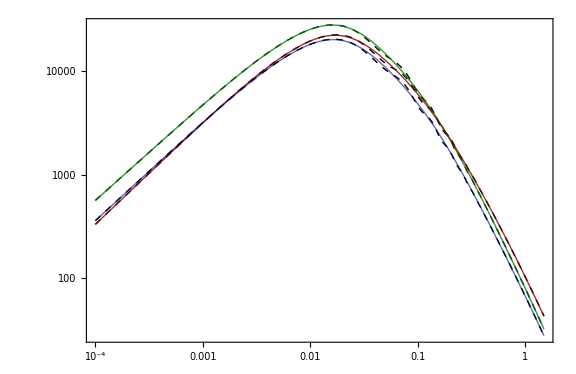

```mathematica
i=1;j=2;l=3;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\log f_{R_0} = -6.922"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\log f_{R_0} = -5.006"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\log f_{R_0} = -6.292"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]}},ImageSize->480]//Quiet
```

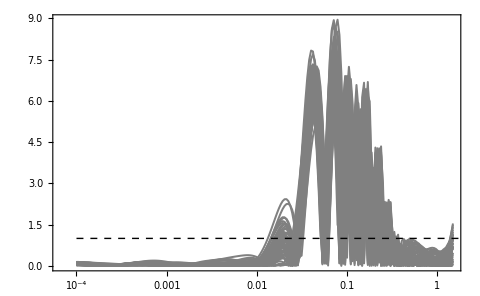

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:=1+(ⅇ^(-1.36418 ((h k)/(0.373 ωb^0.419+0.195 ωm^1.0957))^0.9914) (0.10047-0.1485 ωb^0.76324+0.0005236 ωm^1.49987) Sin[(0.78991 ((h k)/(0.00785436 ωb^0.177084+0.00912388 ωm^0.618711+11.9611 ωb^2.81343 ωm^0.784719)+0.54264282715945/ωm^0.2695499))/(0.7349+1.0058717(1/(h k)(0.00785436 ωb^0.177084 ωm^0.234948+0.00912388 ωm^0.853659+11.9611 ωb^2.81343 ωm^1.019667))^1.19806)^0.739668])/(1.03922+(1/(h k)(0.00785436 ωb^0.177084+0.00912388 ωm^0.618711+11.9611 ωb^2.81343 ωm^0.784719) (1.47345-49.99978 ωb^0.96164+46.02641 ωm^1.24458))^2.7345)
Tsilk[k_]:=1-0.006249*ⅇ^(-((k-0.1994)/0.062686)^2)
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2*Tsilk[k]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

```mathematica
{Mean[#],Min[#],Max[#],Position[#,Min[#]],Position[#,Max[#]]}&@Table[Mean[AccGA[i][[All,2]]],{i,Length[ParamsPMG]}]
```

{0.342183,0.183833,0.780165,{{2}},{{31}}}

### Visual Comparison

{-6.9227,-5.00614,-6.29209}

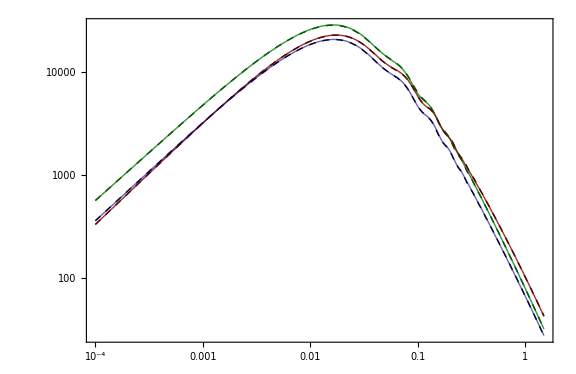

```mathematica
i=1;j=2;l=3;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[1,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[2,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[3,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\log f_{R_0} = -6.922"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\log f_{R_0} = -5.006"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\log f_{R_0} = -6.292"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

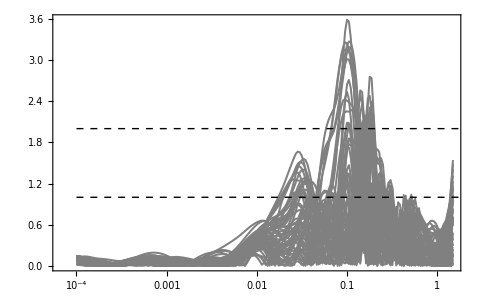

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

# plk_late

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
Import["./Data/cosmo_params_plk_late.txt","Table"][[1]]
Params=Import["./Data/cosmo_params_plk_late.txt","Table"][[2;;-1]];
```

{h,omega_b,omega_m,ns,10^9As,E11,E22}

```mathematica
dir="./Data/spectra_latin_hc_plk_late/";
paths=FileNameJoin[{dir,"spectrum_"<>IntegerString[#,10,3]<>".txt"}]&/@Range[1,Length[Params]];
PkData=Rest[Import[#,"Data"]]&/@paths;
```

## No Wiggles

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
TGAnw[k_,h_,ωb_,ωm_]:=(1+101.855 ((h*k)/(ωm-ωb))^1.483+21112.189((h*k)/(ωm-ωb))^3.972+35913.065  ((h*k)/(ωm-ωb))^6.097+1428.081((h*k)/(ωm-ωb))^7.507)^(-1/4)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,α_,γ_,kMG_,Δ_]:=A0[h,ωm,ns,As]*(1+0.711 α^3+1.880 α^4+0.939 α^5)k^ns*TGAnw[k,h,ωb,ωm]^2(1+γ/(1+(kMG/k)^Δ))
Plarge[k_,h_,ωm_,ns_,As_,s_]:=A0[h,ωm,ns,As]*(1+s)*k^ns; (* Primordial spectrum *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(Log[k]-Log[k0])/β)); (* Transition function *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ] (* Total spectrum *)
```

### Accuracy

```mathematica
χ2Pk[i_][s_,k0_,β_,α_,γ_,kMG_,Δ_]:=Mean[Table[Abs[1-PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/(PkData[[i]][[j,2]])]*100,{j,1,Length[PkData[[i]]]}]];
```

```mathematica
BFχ2Pk[i_]:=NMinimize[χ2Pk[i][s,k0,β,α,γ,kMG,Δ],{s,k0,β,α,γ,kMG,Δ},Method->"DifferentialEvolution",MaxIterations->1000]//Quiet
```

```mathematica
t0=AbsoluteTime[];
ParamsPMG=ParallelTable[BFχ2Pk[i],{i,1,Length[PkData]}];
Print["Time: ", AbsoluteTime[]-t0]
```

Time: 150.58174

```mathematica
PhysicalIndices=Select[ParamsPMG,((k0/. #[[2]])>=0&&(kMG/. #[[2]])>=0)&];
PhysicalIndices//Length
```

12

```mathematica
PrecisePhysicalIndices=Flatten@Position[PhysicalIndices[[All,1]],_?(#<=1.05&)]
PrecisePhysicalIndices//Length
Position[PhysicalIndices[[All,1]],_?(#<2&)]//Flatten//Length
```

{2,3,4,6,7,8,9,10,11,12}

10

12

```mathematica
GetOriginalPosition[physicalList_,originalList_,indexInPhysical_]:=FirstPosition[originalList,physicalList[[indexInPhysical]]][[1]];
```

```mathematica
PreciseIndices=GetOriginalPosition[PhysicalIndices,ParamsPMG,#]&/@PrecisePhysicalIndices
```

{15,26,31,50,59,60,65,70,79,80}

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PMG[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{-0.112643,-0.794964,0.447768}

{0.123795,0.871144,-0.580678}

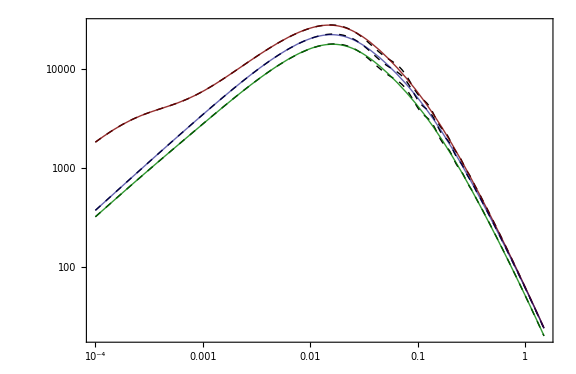

```mathematica
i=15;j=26;l=31;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
{Params[[i,7]],Params[[j,7]],Params[[l,7]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[2,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[3,2]]),
(PMG[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[4,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["E_{11} = -0.113, \\ E_{22} = 0.124"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["E_{11} = -0.795, \\ E_{22} = 0.871"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["E_{11} = 0.448, \\ E_{22} = -0.581"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

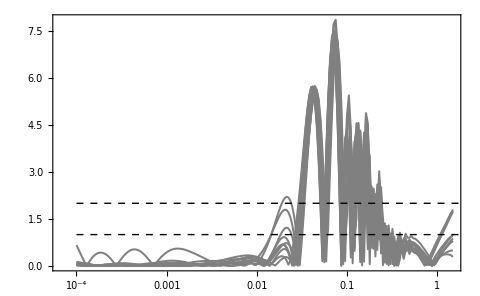

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```

## Adding Wiggles

### Fitting Function

```mathematica
TGAw[k_,h_,ωb_,ωm_]:="1"+(ⅇ^("-1.378" ((h k)/(0.708 ωb^0.547))^("0.925")) ("0.030"+"0.180" ωm^("0.661")) Sin[("0.743" ((h k)/("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785"))+("0.638")/ωm^("0.297")))/(("0.648"+"2.192" ((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ωm^("0.481"))/(h k))^("1.133"))^("0.664"))])/("0.767"+((("0.008" ωb^("0.177")+"0.009" ωm^("0.619")+"11.961" ωb^("2.813") ωm^("0.785")) ("1.025"-"8.639" ωb^("0.500")+"59.992" ωm^("1.353")))/(h k))^("2.622"))
PFull[k_,h_,ωb_,ωm_,ns_,As_,s_,k0_,β_,α_,γ_,kMG_,Δ_]:=(1-σ[k,k0,β])Plarge[k,h,ωm,ns,As,s]+σ[k,k0,β]*Psmall[k,h,ωb,ωm,ns,As,α,γ,kMG,Δ]*TGAw[k,h,ωb,ωm]^2(* Total spectrum *)
```

### Accuracy

```mathematica
AccGA[i_]:=Table[{PkData[[i]][[j,1]],100*Abs[1-1/(PkData[[i]][[j,2]])PFull[PkData[[i]][[j,1]],Params[[i,1]],Params[[i,2]],Params[[i,3]],Params[[i,4]],Params[[i,5]],s,k0,β,α,γ,kMG,Δ]/.ParamsPMG[[i,2]]]},{j,Length[PkData[[i]]]}]
```

### Visual Comparison

{-0.112643,-0.794964,0.447768}

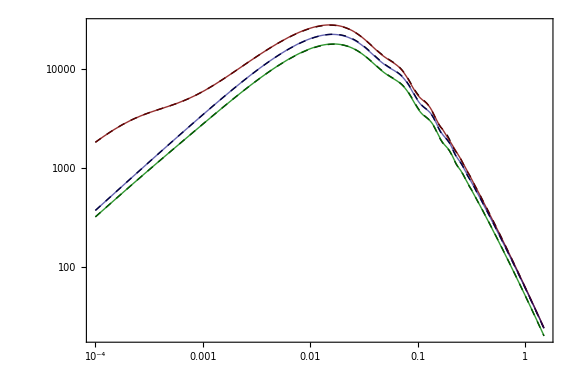

```mathematica
i=15;j=26;l=31;
{Params[[i,6]],Params[[j,6]],Params[[l,6]]}
ListLogLogPlot[{PkData[[i]],PkData[[j]],PkData[[l]]},Joined->True,PlotRange->All,PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,ImageSize->720];
LogLogPlot[{(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[i,1]],ωb->Params[[i,2]],ωm->Params[[i,3]],ns->Params[[i,4]],As->Params[[i,5]]}/.PhysicalIndices[[2,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[j,1]],ωb->Params[[j,2]],ωm->Params[[j,3]],ns->Params[[j,4]],As->Params[[j,5]]}/.PhysicalIndices[[3,2]]),
(PFull[k,h,ωb,ωm,ns,As,s,k0,β,α,γ,kMG,Δ]/.{h->Params[[l,1]],ωb->Params[[l,2]],ωm->Params[[l,3]],ns->Params[[l,4]],As->Params[[l,5]]}/.PhysicalIndices[[4,2]])}//Evaluate,{k,PkData[[1]][[1,1]],PkData[[1]][[-1,1]]},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["E_{11} = -0.113, \\ E_{22} = 0.124"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["E_{11} = -0.795, \\ E_{22} = 0.871"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["E_{11} = 0.448, \\ E_{22} = -0.581"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],ImageSize->Medium];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->All,ImageSize->Large]//Quiet
```

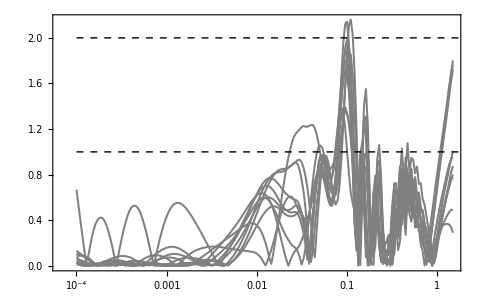

```mathematica
ListLogLinearPlot[AccGA[#]&/@PreciseIndices,Joined->True,PlotRange->All,PlotStyle->{Directive[Thickness[0.003],Gray]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]},{Dashed,Thick,Line[{{Log[10^-4],2},{Log[10],2}}]}},ImageSize->480]//Quiet
```